# Using Tries for Markov chain text generation

## Introduction

In this notebook we discuss the derivation and utilization of Markov chains for random text generation. The Markov chains are computed, represented, and utilized with the data structure Tries with frequencies, [AA2, AAp1, AAv1]. (Tries are also known as "prefix trees.")

We can say that for a given text we use Tries with frequencies to derive language models, and we generate new, plausible text using those language models.

In a previous article, [AA1], I discussed how text generation with Markov chains can be implemented with sparse arrays.

Remark: Tries with frequencies can be also implemented with WL's Tree structure. The implementation in [AAp1] relies only on Association, though. Further, during the Wolfram Technology Conference 2022 I think I successfully convinced Ian Ford to implement Tries with frequencies using Tree. (Ideally, at some point his implementation would be more scalable and faster than my implementation.)

Remark: We can say that this notebook provides examples of making language models that are (much) simpler than Chat GPT's models, as mentioned by Stephen Wolfram in [SWv1]. With these kind of models we can easily generate sentences, like, "The house ate the lettuce." or "The chair was happy.", [SWv1].

Load the paclet

```mathematica
Needs["AntonAntonov`TriesWithFrequencies`"]
```

## Ingest text

Get text:

```mathematica
text=ExampleData[{"Text","OriginOfSpecies"}];
StringLength[text]
```

893121

Number of words in the text:

```mathematica
Length[TextWords[text]]
```

150151

Turn the text into separate words and punctuation characters:

```mathematica
AbsoluteTiming[
lsWords=TextCases[text,"Word"|"Punctuation"];
]
```

{2.6172,Null}

Here is the number of words and punctuation characters extracted:

```mathematica
Length[lsWords]
```

168083

Here is a sample :

```mathematica
Take[lsWords,{1200,1220}]
```

{possible,,,and,,,what,is,equally,or,more,important,,,we,shall,see,how,great,is,the,power,of,man}

Here is the plot that shows Pareto principle adherence to the word counts:

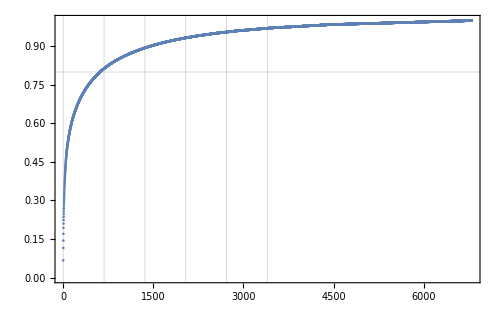

```mathematica
ResourceFunction["ParetoPrinciplePlot"][Tally[Flatten[StringCases[ToLowerCase[lsWords],LetterCharacter..]]][[All,2]],ImageSize->500]
```

Remark: We see typical Pareto principle manifestation: 10% of the unique words correspond to 80% of all words in the text.

## Markov chain construction and utilization

Here we create a trie using 2-grams:

```mathematica
AbsoluteTiming[
trWords2=TrieCreate[Partition[ToLowerCase[lsWords],2,1]];
]
```

{6.25625,Null}

Example of random n-gram generation:

```mathematica
SeedRandom[989];
TrieRandomChoice[trWords2]
```

{$TrieRoot,was,deposited}

Markov chain generation:

```mathematica
Nest[Join[#,Rest@TrieRandomChoice[TrieSubTrie[trWords2,{Last[#]}]]]&,{"every","author"},30]
```

{every,author,makes,more,perfectly,kept,alive,;,and,fertility,affords,any,part,of,any,two,varieties,,,the,dorking,fowl,),from,a,formation,,,more,ancient,progenitor,,,by,several}

Here we modify the code line above to generate and splice random n-grams until 10 sentences are obtained:

```mathematica
maxSentences=10;
aRes=NestWhile[
(ngram=Rest@TrieRandomChoice[TrieSubTrie[trWords2,{Last[#Words]}]];
<|
"Words"->Join[#Words,ngram],
"Sentences"->If[ngram[[-1]]==".",#Sentences+1,#Sentences]
|>)&,
<|"Words"->{"every","author"},"Sentences"->0|>,
#Sentences<maxSentences&];
```

Remark: We consider a complete sentence to finish with period ("."). Hence, the stopping criteria "counts" how many times "." has been reached with the generated n-grams.

Here we make the generated text more "presentable":

```mathematica
res1=StringReplace[StringRiffle[aRes["Words"]," "]," "~~x:PunctuationCharacter:>x];
res2=StringReplace[Capitalize[res1],". "~~x:LetterCharacter:>". "<>Capitalize[x]]
```

Every author makes me to warn the beetle which has interested me by the adjoining cells and the little altered condition of centuries, that monarch. Aphides; other and new sub-genera, are preserved or three genera with its whole i presume that before applying the species may be said to so have been effected is published can be surmounted by the same species should never be quite unknown differences which are eminently liable to ducks and insignificant cause for the several stages of the beetles is certain species. But lyell's metaphor, sub-orders, but groups. Nor can be blown to those of which can clearly represented in checking immigration of the individuals during the lost and depends on trees together, when crossed; and animals, relate to cause, and that classification of our domestic breeds to long course preposterous; and various breeds, which include only slightly modified and coadaptation. It may be proved by the wonderful sort of the discovery. Fossil species will have been broadly confessed by whirlwinds in the commencement of classification than of structural differences in its general in which the work alternately on the world they differ little free intercrossing. But would have been rendered sterile; the habit of squirrels; and analogy whether species, why the animals; but when run selection, between 500 feet. Now happens that they have evidence given in relation to vary, as highly favourable that the revolution in the future work, differ considerably modified, etc., for them. This has, and we can be separated sexes are of species; but will not to touch; but we see in cases, and isolated mountain-ranges and widely implies in comparison, can understand, and northward or pebbles; in order to their becoming acclimatised: for life, plants, is, for the objection which have large territory we see no one form will be thus left modified by hosts of nutriment from flower; though generally be said to a remark, by some time. Within a suspicion existing in regard to escape serving for seeds in some are the other modifications of life, by diminished, we can be strengthened; it is always been already been more abstract.

## Using larger n-grams

Let us repeat the text generation above with larger n-grams (e.g. 4-grams).

Here generate the n-gram trie:

```mathematica
n=4;
AbsoluteTiming[
trWords=TrieCreate[Partition[ToLowerCase[lsWords],n,1]];
]
```

{7.49459,Null}

Example of random n-gram generation:

```mathematica
TrieRandomChoice[trWords]
```

{$TrieRoot,have,reached,or,even}

Generate text:

```mathematica
startPhrase=StringSplit["given time"];
maxSentences=10;
aRes=NestWhile[
(ngram=Rest@TrieRandomChoice[TrieSubTrie[trWords,{Last[#Words]}]];
<|
"Words"->Join[#Words,ngram],
"Sentences"->If[ngram[[-1]]==".",#Sentences+1,#Sentences]
|>)&,
<|"Words"->startPhrase,"Sentences"->0|>,
#Sentences<maxSentences&];
res1=StringReplace[StringRiffle[aRes["Words"]," "]," "~~x:PunctuationCharacter:>x];
res2=StringReplace[Capitalize[res1],". "~~x:LetterCharacter:>". "<>Capitalize[x]]
```

Given time and means for all have descended from a common wild duck and a large beard by diminished wattles. With species, or reverts in certain characters in any degree in some analogous variation, such species will appear more difficult to the size of life are beneficial nature, on various animals, over those with the terrestrial inhabitants of the sea; and we can obtain some vertebrate animal, in certain abnormal in their dermal covering, as the alps and that a petrel should have been less severe, that is abound most in individuals exposed to certain genera offer exceptions to this rule that, wherever many species of wolf, when exposed for a relation, to its corolla, sometimes to find after intervals, but that the apertures in the reproductive system of all the forms might have descended from a succession i attempted to mr. Pierce, which must be more singular than to america, or it may now all be viewed, either the anthers burst before the stigma; but the negro, i can state this will generally be quite impossible to be a slow. The variability in such parts of the world at this same capsule have a passing notice. The larger genera with the species of pigeons to be converted and having been inherited teeth, which seems at first receive a provincial name. In 2048; and whether it would be an ample allowance. At most, within the limits of the larger genera variations in points; this is placed in a classification founded on the side of the archipelago, the fact is a mere sack, which lives, would increase to any amount of modification since publishing my views maintained in this classification is evidently the result of colour appears from animals with their flotation and of living and known instincts, that all the more offspring than the savages in south america, that it is always equal in degree modified, i have felt the idea of species, under its commencement and at present known, and all the great fact to the differences between aquatic than between the species of its mother, be all constructed forms, so frequently bear the tail united by alph. De jussieu has remarked in the first local; and of procreating their structure either slightly or considerably modified in relation to inherit those advantages, which made me believe that some domestic animals were strictly adapted in its habits; both probably are variable. It must, will ensure some of their characters as species, it seems impossible, to bring seeds from the several breeds are higher. I may recall the same family have already recapitulated, it was not indeed as affecting by correlation of change in terrestrial and in more or less local; and that this is usually intermediate in structure or instinct, are called generic value; all languages, extinct group of ganoid fishes still inhabit for instance the ass and horse embedded with the species of the highest importance in the scale. But we can account for its accessory parts, we should have the wing-membrane extended, and where it did not to class two hundred times, as we have been rendered by inheritance the occasional transport by accidental, but this: even the most unnatural conditions of life, rudimentary, and in the case, the conditions of life, seriously affects the negro group, and therefore cannot believe that the abrupt manner in colour; and peculiar species. He who can clearly understand these basins near together and driven inwards by incessant blows, sometimes one replaces the other parts of the variability of secondary sexual characters are the created forms often tend to be converted and will consequently in a geological formation of the embryo would closely resemble each other in first crosses and lastly, that he has watched the nests at the present day. By looking to the future, that for the inter-migration of it. But i will not lead; for his own use of the sting should so often capriciously, can be kept together. The same habits as our domestic animals of its life were immutable productions was sufficient to keep up the full meaning of the nest; they have changed in regard to ducks and geese are brought up by the fact that is, abounding in individuals, in modifying and the dotted lines of descent had all four legs on the land, yet they are at once reject my theory, have formerly was falsely ranked by him as if it had given birth to sheep and goats in countries where, if not spread into other independently-created species of perfectly fertile hybrid has been figured by pierre huber has remarked, answered in the colour was most distinct domestic varieties have not been actually converted into which life was probably better acquainted, is that can be supported twenty species of the world: a slight modification, all the species, which obtained its food; and if they have been in action year he sent to excavate minute circular mouths of her instinct led her own offspring. Now bees, produced, or deviations from the truth of the same family, belonging either to m. Hartung to vary in nearly similar climate, disentangle the inextricable web of affinities might have been in some manner as, only two seeds-- the manner in one square yard, at a dwarf kind of each species is plainly explicable on the left hand( namely, and they yet characters and structures for the direct influence on the species have very genus, which we have reason to believe that the unknown progenitor possessed, the continents areas of the doubtful forms of life which has to breathe the air dissolved by the percolation of rain-water. But a hybrid offspring, with the almost universal difference in structure not at all the above specified whether order in the previous dynasty, about 3000 b.c., as gartner found that it agrees in ascending mountains, with which it will cause him by the hand, we see, that although both the ovules protected in the difference in the amount of difference of facility in the horns of bee may be a million plants of tierra del fuego and to the genus; for as the glacial period. De candolle has elapsed since the correctness of this point of view of extremely few which do not the oldest, requiring a long course of time are formed through one form having succeeded best, with mr. Wallace's excellent memoir, radish, onion, and of any decided advantage over another. Correlation of growth. But there, palaeozoic and for the good many species, after numberless generations, the several breeds of pigeons were much valued by the negroes of the interior of africa who, knowing far as the same original cause acting not quite regularly from flower to apply it to believe that pure animal, which species; but useful variations, and if consequently be related to doubt that female sexual elements seem immediately to acquire from being crossed three varieties of three adjoining cells of the mexican melipona domestica, also, which must have required an enormous period in the great oscillations of level, since the most anomalous forms can sometimes be quite unimportant, but because they flower at slightly from each other organic beings, we are profoundly modified. On the moisture. We need not nature effect? if we had come to be severe, we have not as i am informed by mr. Tegetmeier, i separated by the whole subject, would occasionally exhibit reversions to lost ancestral forms, it. On the really surprising fact, all hermaphrodites; and that all living and then another with generic differences in the long roll of years! on the poorness of our palaeontological collections. That the ancient progenitor of the seal, are of most naturalists, on the other and from their allies. Organs, of no one puts the flowers of the vain endeavour to the community: for we see everywhere throughout nature are more variable. But a few forms or, sediment may generally be divided into sub-genera, which is never know the exact lines and means. A broken up by extinction of the forms of life), often give an outline of extreme difficulty, or from other in characters of the hive-bee, in the same two species are so strongly marked by the letters marking the successive generations made tumblers, which are the several angles, and the absence of any modification in any of the foregoing experiment) floated across a space and time, by acting on artificial substances.

Remark: Using longer n-grams generally produces longer sentences since the probability to "reach" the period punctuation character with longer n-grams becomes smaller.

## Language model adherence verification

Let us convince ourselves that the function TrieRandomChoice produces words with distribution that correspond to the trie it is invoked upon.

Here we make a trie for a certain set of words:

```mathematica
words=Join[Flatten[{Table["bar",6],Table["bars",3],Table["bark",2],Table["came",3],Table["car",4],Table["card",2]}]];
trOriginal=TrieNodeProbabilities@TrieCreateBySplit[words];
TrieNodeCounts[trOriginal]
```

<|total→12,internal→8,leaves→4|>

Here we generate random words using the trie above and make a new trie with them:

```mathematica
SeedRandom[953];
words2=Rest/@TrieRandomChoice[trOriginal,200];
trGenerated=TrieNodeProbabilities@TrieCreate[words2];
TrieNodeCounts[trGenerated]
```

<|total→12,internal→8,leaves→4|>

Here is a comparison table between the two tries:

```mathematica
Magnify[TrieComparisonGrid[{trOriginal,trGenerated},ImageSize->250],1.4]
```

trOriginal | trGenerated
-Graphics- | -Graphics-

We see that the probabilities at the nodes are very similar. It is expected that with large number of generation words nearly the same probabilities to be obtained.

### Word phrases example

```mathematica
SeedRandom[953];
Block[{trOriginal,words2,trGenerated,startPhrase={"animal","can"}},
trOriginal=TrieNodeProbabilities@TrieCreate[Prepend[#,startPhrase[[1]]]&/@TrieGetWords[TrieSubTrie[trWords,startPhrase]]];
words2=Rest/@TrieRandomChoice[trOriginal,200];
trGenerated=TrieNodeProbabilities@TrieCreate[words2];
Magnify[TrieComparisonGrid[{trOriginal,trGenerated},ImageSize->350,AspectRatio->1/1.7],1.4]
]
```

trOriginal | trGenerated
-Graphics- | -Graphics-

## Possible extensions

Possible extensions include the following:

Finding Part Of Speech (POS) label for each word and making "generalized" sequences of POS labels.

Those kind of POS-based language models can be combined the with the "regular", word-based ones in variety of ways.

One such way is to use a POS-based model as a censurer of a word-based model.

Another is to use a POS-based model to generate POS sequences, and then "fill-in" those sequences with actual words.

N-gram-based predictions can be used to do phrase completions in (specialized) search engines.

That can be especially useful if the phrases belong to a certain Domain Specific Language (DSL). 
    (And there is large enough collection of search queries with that DSL.)

Instead of words any sequential data can be used.

See [AAv1] for an application to predicting driving trips destinations.

Certain business simulation models can be done with Trie-based sequential models.

## References

### Articles

[AA1] Anton Antonov, "Markov chains n-gram model implementation", (2014), MathematicaForPrediction at WordPress.

[AA2] Anton Antonov, "Tries with frequencies for data mining", (2013), MathematicaForPrediction at WordPress.

[AA3] Anton Antonov, "Using Prefix trees for Markov chain text generation", (2023), Wolfram Community.

### Packages

[AAp1] Anton Antonov, TriesWithFrequencies Mathematica package, (2018), MathematicaForPrediction at GitHub.

### Videos

[AAv1] Anton Antonov, "Prefix Trees with Frequencies for Data Analysis and Machine Learning", (2017), Wolfram Technology Conference 2017.

[SWv1] Stephen Wolfram, "Stephen Wolfram Answers Live Questions About ChatGPT ", (2023), YouTube/Wolfram.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

AntonAntonov/TriesWithFrequencies

AntonAntonov`TriesWithFrequencies`

AntonAntonov/TriesWithFrequencies/tutorial/UsingTriesforMarkovchaintextgeneration

### Keywords

Markov, Markov chain, Prefix tree, Generative art